25

0.25

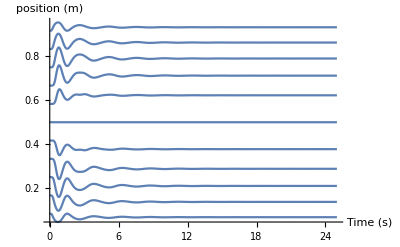

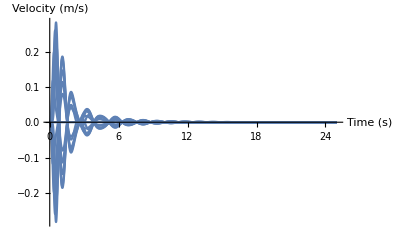

```mathematica
(* Adam Smith *) 
(* 11-27-2017 *)
(* Numerical Mehtods *)
(* Project 1 *)

ClearAll["Global`*"]

(* Constants *)
g = -9.81;       (* Gravitational Constant (m/s^2) *)
size = Scaled[0.8];
(* Denfining Given Variables *)
l   = 1;			(* Length of Bungee Cord (m) *) 
n = 13;		        (* Number of point-masses in Mass-Spring-Damper system *)
lr = l/(n-1);	 (* Distance between point masses (m) *)
ks=100 ;                        (* Spring constnat/Mass (N/m.kg) *)	
kd=10;                            (* Spring constnat/Mass (N/m.kg) *)

Subscript[x, 1][t]=0;
Subscript[x, n][t]=l; 
Subscript[y, 1][t]=0;
Subscript[y, n][t]=0; 
Subscript[x, 1]'[t]=0;
Subscript[x, n]'[t]=0; 
Subscript[y, 1]'[t]=0; 
Subscript[y, n]'[t]=0;

(* Defining the x and y position of point-mass i *)
positionxi = Subscript[x, i][0] ==lr(i-1); 
velocityxi = Subscript[x, i]'[0]==0;
positionyi = Subscript[y, i][0]==0;
velocityyi = Subscript[y, i]'[0]==0;

(* Defining the necessary equations used in Newton's 2^nd Law *)
(* Below are the equations used to solve for the instantaneous position between point-masses *)
pm1[t]  =Sqrt[(Subscript[x, i][t]-Subscript[x, i-1][t])^2+(Subscript[y, i][t]-Subscript[y, i-1][t])^2]; (* Instantaneous position of mass behind i (Subscript[p, i-1]) *)
pp1[t]  =Sqrt[(Subscript[x, i][t]-Subscript[x, i+1][t])^2+(Subscript[y, i][t]-Subscript[y, i+1][t])^2]; (* Instantaneous position of mass behind i (Subscript[p, i+1]) *)

(* Defining Newton's 2^nd Law *)
(* Because this equation can be used to solve both the position and velocity of x and y  I wrote two seperate differential equations to represent each *)
(*Subscript[x, i]''[t]==-ks*(pm1[t]-lr)*(Subscript[x, i][t]-Subscript[x, i-1][t])/pm1[t]-ks*(pp1[t]-lr)*(Subscript[x, i][t]-Subscript[x, i+1][t])/pp1[t]-kd*(Subscript[x, i]'[t]-Subscript[x, i-1]'[t])-kd*(Subscript[x, i]'[t]-Subscript[x, i+1]'[t]);
Subscript[y, i]''[t]==-ks*(pm1[t]-lr)*(Subscript[y, i][t]-Subscript[y, i-1][t])/pm1[t]-ks*(pp1[t]-lr)*(Subscript[y, i][t]-Subscript[y, i+1][t])/pp1[t]-kd*(Subscript[y, i]'[t]-Subscript[y, i-1]'[t])-kd*(Subscript[y, i]'[t]-Subscript[y, i+1]'[t])+g;*)
DifferentialEquation=Table[{Subscript[x, i]''[t]==-ks*(pm1[t]-lr)*(Subscript[x, i][t]-Subscript[x, i-1][t])/pm1[t]-ks*(pp1[t]-lr)*(Subscript[x, i][t]-Subscript[x, i+1][t])/pp1[t]-kd*(Subscript[x, i]'[t]-Subscript[x, i-1]'[t])-kd*(Subscript[x, i]'[t]-Subscript[x, i+1]'[t]),positionxi,velocityxi,
Subscript[y, i]''[t]==-ks*(pm1[t]-lr)*(Subscript[y, i][t]-Subscript[y, i-1][t])/pm1[t]-ks*(pp1[t]-lr)*(Subscript[y, i][t]-Subscript[y, i+1][t])/pp1[t]-kd*(Subscript[y, i]'[t]-Subscript[y, i-1]'[t])-kd*(Subscript[y, i]'[t]-Subscript[y, i+1]'[t])+g , positionyi , velocityyi },{i,2,(n-1)}];


(* Initial Conditions for 1^st set of initial condition *)
(*    1. Velocity of the Spring-Mass_Damper System = 0 at time t = 0.
  2. Stretch of the Bungee Cord = 0 at time t = 0.
 3. The x and y position and velocity of point masses 1, and 13 = 0 at t = 0. 
   4. The system falls under the influence of only the gravitational force *)
(* Using the differential equations defined above the position and velocity of x are solved below *)

time = 25
timeinterval = 0.25

position1x=NDSolve[{DifferentialEquation},Table[{Subscript[x, i][t]},{i,2,(n-1)}],{t,0,time,timeinterval}];
positionx= Evaluate[Table[{Subscript[x, i][t]},{i,2,(n-1)}]/.position1x];
Plot[positionx,{t,0,time},AxesLabel->{"Time (s)","position (m)"},PlotRange->{{0,time},All},ImageSize->size,Frame->False] 


velocity1x= NDSolve[{DifferentialEquation},Table[{Subscript[x, i]'[t]},{i,2,(n-1)}],{t,0,time,timeinterval}]; 
velocityx = Evaluate[Table[{Subscript[x, i]'[t]},{i,2,(n-1)}]/.velocity1x];
Plot[velocityx,{t,0,time},AxesLabel->{"Time (s)","Velocity (m/s)"},PlotRange->{{0,time},All},ImageSize->size,Frame->False] 













(* Initial Conditions for 2^nd set of initial condition *)
(*   1. Velocity of the Spring-Mass-Damper System at time t = 0 has an parabolic upward velocity with a peack value of 10m/s.
 2. The x and y position and velocity of point masses 1, and 13 = 0 at t = 0. *)






















(* Initial Conditions for 3^rd set of initial condition *)
(*    1. Velocity of the Spring-Mass_Damper System = 0 at time t = 0.
  2. The x and y position and velocity of point masses 1 and 13 = 0 at t = 0.
3. The initial y position of point mass 7 = 0.5m at t = 0. *)
```